```mathematica
(* List of fast Deleglise-Rivat alpha factors for x ≤ 10^23 found by running pi(x) benchmarks using the find_fastest_alpha.sh script *)

alphaDelegliseRivat =  { (* {x, alpha} *) {1, 1}, {10^1, 1}, {10^2, 1},{10^3, 1},{10^4, 1.095},{10^5, 1.174},{10^6,1.310}, {10^7,1.591},{10^8,2.278},{10^9,3.455},{10^10,4.125},{10^11,5.195}, {10^12,6.960}, {10^13, 8.272},  {10^14, 11.462}, {10^15,  15.619}, {10^16, 18.980}, {10^17, 22.677}, {10^18,26.246}, {10^19,30.635},{10^20, 36.120},{10^21,42}, {10^22,48.148}, {10^23, 54.832},{10^24,62.66} }
```

{{1,1},{10,1},{100,1},{1000,1},{10000,1.095},{100000,1.174},{1000000,1.31},{10000000,1.591},{100000000,2.278},{1000000000,3.455},{10000000000,4.125},{100000000000,5.195},{1000000000000,6.96},{10000000000000,8.272},{100000000000000,11.462},{1000000000000000,15.619},{10000000000000000,18.98},{100000000000000000,22.677},{1000000000000000000,26.246},{10000000000000000000,30.635},{100000000000000000000,36.12},{1000000000000000000000,42},{10000000000000000000000,48.148},{100000000000000000000000,54.832},{1000000000000000000000000,62.66}}

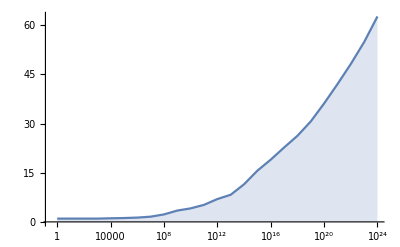

```mathematica
ListLogLinearPlot[alphaDelegliseRivat,Filling->Bottom, Joined-> True]
```

```mathematica
(* alpha is a tuning factor that balances the compuation of the easy special leaves and the hard special leaves. The formula below is used in the file src/primecount.cpp to calculate a fast alpha factor for the computation of pi(x). *)

NonlinearModelFit[alphaDelegliseRivat, a(Log[x])^3 + b (Log[x])^2 + c Log[x] + d, {a,b, c, d}, x]
```

FittedModel[1.39952-0.125227 Log[x]+0.00263762 Log[x]^2+0.000356618 Log[x]^3]

```mathematica
(* Below is another formula which is quite accurate for calculating the
 Deleglise-Rivat alpha factor in primecount. The constant 2200 has
 been obtained by running many pi(10^20) benchmarks. *)

alpha[x_] := (Log[x])^3 / (2200 (Log[Log[10^20]] / Log[Log[x]])^3)
```

```mathematica
(* List of fast Lagarias-Miller-Odlyzko alpha factors found by running pi(x) benchmarks. *)

alphaLMO = {(* {x, alpha} *) {1, 1},{10^10, 1.208}, {10^11, 1.281},  {10^12, 1.364},{10^13, 1.679},{10^14, 1.890},{10^15,2.011},{10^16, 2.113},{10^17, 2.359},{10^18, 2.556}}
```

{{1,1},{10000000000,1.208},{100000000000,1.281},{1000000000000,1.364},{10000000000000,1.679},{100000000000000,1.89},{1000000000000000,2.011},{10000000000000000,2.113},{100000000000000000,2.359},{1000000000000000000,2.556}}

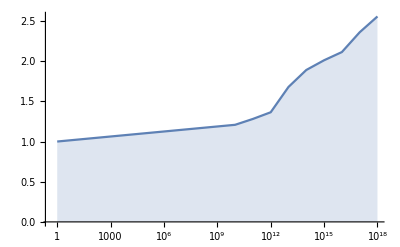

```mathematica
ListLogLinearPlot[alphaLMO,Filling->Bottom, Joined-> True]
```

```mathematica
(* alpha is a tuning factor that balances the compuation of the easy special leaves and the hard special leaves. The formula below is used in the file src/primecount.cpp to calculate a fast alpha factor for the computation of pi(x). *)
```

```mathematica
NonlinearModelFit[alphaLMO, a(Log[x])^2 + b  Log[x] + c, {a,b, c}, x]
```

FittedModel[0.990948-0.0261411 Log[x]+0.00156512 Log[x]^2]